# Leitercharakteristik

## Aufgabe 1

```mathematica
nbasis[n_Integer][x_]:=Table[x^k,{k,0,n}]
```

```mathematica
Needs["ErrorBarPlots`"];
```

Drahtwiderstand 15 kΩ - 10 ± 5 %

```mathematica
V={11.15, 19.76, 30.99, 40.5, 49.9, 59.9, 80.1, 99.9, 120.1, 139.6, 160.9, 179.9, 199.8, 220.1, 239.0, -21.9, -39.3, -61.3, -80.2, -100.4, -119, -140.3, -160.3, -180.4, -200.3, -220.9, -238.5,0};
```

±0.07 in V

```mathematica
A={0.759, 1.35, 2.098, 2.754, 3.38, 4.065, 5.427, 6.762, 8.125, 9.448, 10.865, 12.142, 13.475, 14.82, 16.065, -1.48, -2.659, -4.152, -5.444, -6.8, -8.056, -9.491, -10.846, -12.187, -13.518, -14.878, -16.077,0};
```

±0.01 in mA

```mathematica
data = Table[{V[[i]],A[[i]]},{i,1,Length[V]}];
```

```mathematica
fit = Fit[data,nbasis[1][x], x];
```

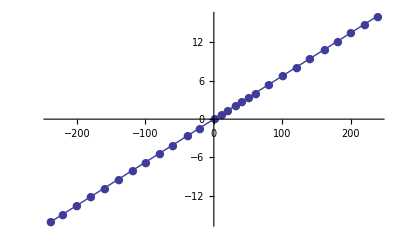

```mathematica
Show[ListPlot[Table[{V[[i]],A[[i]]},{i,1,Length[V]}],PlotMarkers->{Automatic,Tiny}], Plot[fit,{x,Min[V],Max[V]}]]
```

Metallfadenlampe 10 W

```mathematica
V={19.38,   39.5, 60.8,  80.1, 99.4, 120.5, 140.4, 160.5, 180.5, 199.9, 221.1, 239.5, -239.5, -219.1, -199.8, -180.8, -159.5, -139.0, -120, -100.6 ,-80.7, -59.6, -41.5, -19.86,0};
```

±? in V

```mathematica
A={9.535, 14.798, 19.254, 22.763, 25.939, 29.11, 31.94, 34.54, 37.02, 39.39, 41.74, 43.75, -43.72, -41.51, -39.3, -37.02, -34.36, -31.71, -29.01, -26.109, -22.832, -19.023, -15.283, -9.651,0};
```

±? in mA

```mathematica
data = Table[{V[[i]],A[[i]]},{i,1,Length[V]}];
```

```mathematica
fit = Fit[data,nbasis[3][x], x];
```

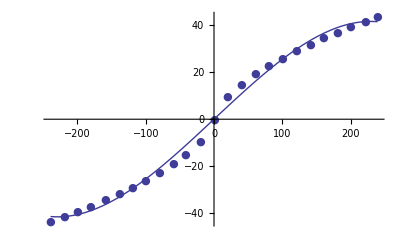

```mathematica
Show[ListPlot[Table[{V[[i]],A[[i]]},{i,1,Length[V]}],PlotMarkers->{Automatic,Tiny}], Plot[fit,{x,Min[V],Max[V]}]]
```

Kohlenfadenlampe 35 W

```mathematica
V={20.7,  39.9, 59.3, 80.4, 99.0, 119.8,140.0, 159.5, 179.5, 202.2, 210.2, -210.4, -199.5, -179.8, -160.8, -139.5, -120.7, -99.5, -80.4, -60.9, -40.4, -20.25,0};
```

±0.05 in V

```mathematica
A={14.032, 28.645, 44.95, 63.97, 81.97, 103.20, 124.88, 147.05, 170.75, 198.95, 209.06, -203.90, -195.51, -171.05, -148.50, -124.31, -104.09, -82.34, -63.95, -46,-31, -29.06, -13.728,0};
```

±0.005 in mA

```mathematica
data = Table[{V[[i]],A[[i]]},{i,1,Length[V]}];
```

```mathematica
fit = Fit[data,nbasis[3][x], x];
```

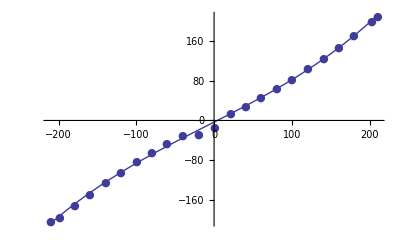

```mathematica
Show[ListPlot[data,PlotMarkers->{Automatic,Tiny}], Plot[fit,{x,Min[V],Max[V]}]]
```

Silizium - Diode max 400 V

```mathematica
V={-19.65, -40.4, -59.2, -81.0, -99.8, -120.2, -139.1, -161.0, -180.7, -200.3, -221.2, -233.95, 0.771, 0.749, 0.694, 0.635,0};
```

±? in V

```mathematica
A={-1.95, -4.06, -5.94, -8.12, -10.01, -12.01, -13.94, -16.12, -18.00, -20.09, -22.15, -23.98, 206500, 119400, 31000, 7700,0};
```

±? in μA

```mathematica
data = Table[{V[[i]],A[[i]]},{i,1,Length[V]}];
```

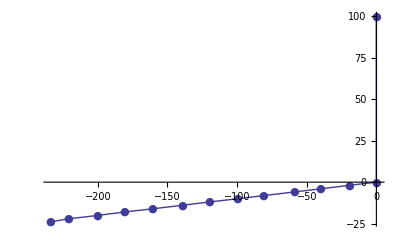

```mathematica
ListPlot[Sort[data,#1[[1]]<#2[[1]]&],Joined->True, PlotRange->{{Min[V],Max[V]},{Min[A], 100}},Joined->True,PlotMarkers->{Automatic,Tiny}]
```

Zenerdiode

```mathematica
V={20.5, 41.2, 60.8, 80.0, 99.9, 120.7, 140.1, 160.0, 180.8, 196.2,188.9,  189.1,189.4,  185.2, 187.0,  187.7, 188.3, -0.693, -0.668, -0.620,0};
```

±0.07 in V

```mathematica
A={2.02, 4.13, 6.08, 7.98, 10.03, 12.06, 14.00, 15.99, 18.08, 4843, 170, 385, 504, 18.5, 18.69, 18.77, 55, -20690, -12894, -3655,0};
```

±0.01 in μA bis 180V

```mathematica
data = Table[{V[[i]],A[[i]]},{i,1,Length[V]}];
```

```mathematica
Sort[data,#1[[1]]<#2[[1]]&]
```

{{-0.693,-20690},{-0.668,-12894},{-0.62,-3655},{0,0},{20.5,2.02},{41.2,4.13},{60.8,6.08},{80.,7.98},{99.9,10.03},{120.7,12.06},{140.1,14.},{160.,15.99},{180.8,18.08},{185.2,18.5},{187.,18.69},{187.7,18.77},{188.3,55},{188.9,170},{189.1,385},{189.4,504},{196.2,4843}}

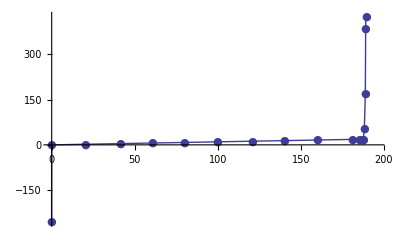

```mathematica
ListPlot[Sort[data,#1[[1]]<#2[[1]]&],Joined->True,PlotMarkers->{Automatic,Tiny}]
```

Glimmstabilisator 78V max 60mA

```mathematica
V={0,19.98, 40.7, 60.9, 79.3, 99.7, 88.8,92.7,89.0,  89.9, 90.4, 91.2};
```

±? in V

```mathematica
A={0,1.97, 4.09, 6.09, 7.92, 9.95, 4.34,13747,  28943, 40260, 49030, 56750};
```

±? in μA

glühen bei 88.8 V

```mathematica
data = Table[{V[[i]],A[[i]]},{i,1,Length[V]}];
```

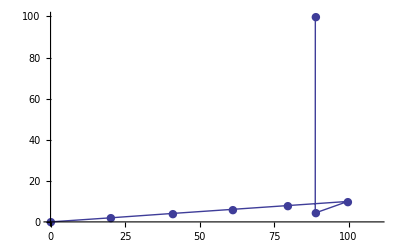

```mathematica
ListPlot[data, PlotRange->{{0,Max[V]*1.1},{0,100}},Joined->True,PlotMarkers->{Automatic,Tiny}]
```

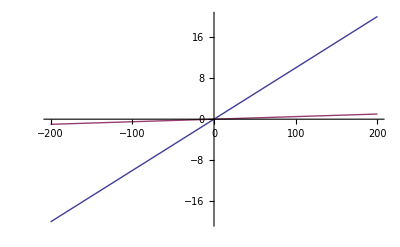

```mathematica
Plot[{u/10,u/200},{u,-200,200}]
```